## First some definitions

```mathematica
Clear[CollatzLine];
```

```mathematica
CollatzLine2[start_, done_:{}]:=Block[{current=start,next, result={}},
While[current≠1,
next=If[Mod[current,2]==0,current/2,(current*3+1)/2];
AppendTo[result,next ->current];
If[MemberQ[done,next],
current=1,
current=next
];
];
result
]
```

```mathematica
FileNameFor[max2_]:="c:\\Saved\\collatz"<>ToString[max2]<>".m"
```

```mathematica
Clear[CollatzForest2];CollatzForest2[max2_]:=CollatzForest2[max2]=Block[
{
 result,current, toAdd,pow=2^max2, file=FileNameFor[max2],order=Max[4,N[Log[10,2^max2]]//IntegerPart],
todo, done=0,started, elapsed,eta
},
If[FileExistsQ[file],
PrintTemporary["Loading "<> file];
result=Get[file]
,
todo=pow;
If[max2==1,
result=Graph[{1},{1->2}];,
result=CollatzForest2[max2-1];
];
Print[todo];
started=AbsoluteTime[];
Monitor[
For[current=1,current≤pow,current++,
If[!VertexQ[result,current],
toAdd=CollatzLine2[current,VertexList[result]];
Table[If[!EdgeQ[result,edge],result=EdgeAdd[result,edge]],{edge,toAdd}];
done++
,
todo--
]
],
elapsed=(AbsoluteTime[]-started);
eta=(elapsed/done)*todo;
Row[{"Level ",max2, " ",ProgressIndicator[current,{1,pow}]," ",N[current/pow*100,order],"%", "  ",current, " of " , pow," ",done,"/",todo," " , elapsed, "  ETA= ",  DateString[ started+eta]}]
];
PrintTemporary["Saving "<> file];
Put[result,file];
];
result
]
```

```mathematica
CollatzLine2[27,{31}]
```

{41→27,62→41,31→62}

```mathematica
CountConnected2[x_,a_,aMax_]:=CountConnected2[x,a]=Block[{g=CollatzForest2[aMax], out, pow=2^a},
out=VertexOutComponent[g,x];
Select[out,#≤pow&]//Length
]
```

## TEst the methods

```mathematica
g=CollatzForest2[18];VertexCount[g]
```

131072

262144

$Aborted

## Now some calcs

```mathematica
Table[CountConnected2[k,10,10],{k,1,100}]
```

{1024,1023,9,1022,954,8,165,1021,7,944,419,7,469,164,7,66,449,6,172,943,6,253,434,6,30,468,6,156,237,6,81,65,5,29,454,5,137,171,5,473,46,5,55,252,5,426,166,5,107,29,5,18,464,5,39,155,5,64,59,5,399,80,5,58,100,4,75,28,4,19,175,4,28,136,4,140,57,4,11,472,4,39,57,4,27,54,4,14,69,4,262,425,4,84,48,4,16,106,4,23}

```mathematica
Table[Table[CountConnected[k,pow],{k,1,100}],{pow,2,15}]//MatrixForm
```

$Aborted

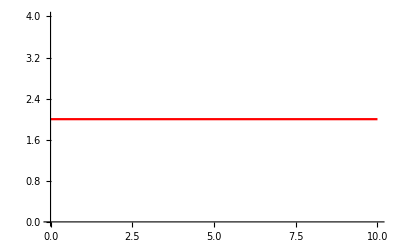

```mathematica
Plot[2,{x,0,10}, PlotStyle->Red]
```

```mathematica
Select[Range[1000,1030],!Divisible[#,3]&]
```

{1000,1001,1003,1004,1006,1007,1009,1010,1012,1013,1015,1016,1018,1019,1021,1022,1024,1025,1027,1028,1030}

Divide::indet: Indeterminate expression 0/0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 3/0 encountered.

Divide::infy: Infinite expression 2/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

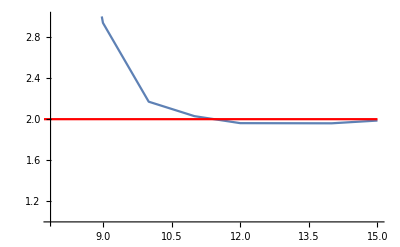
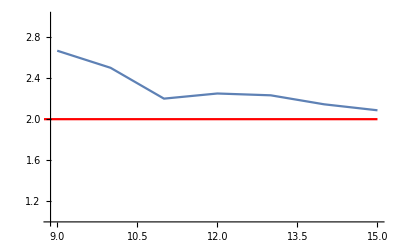
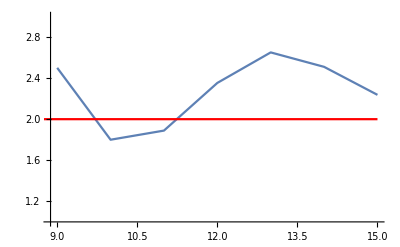
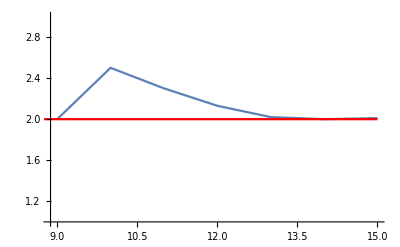
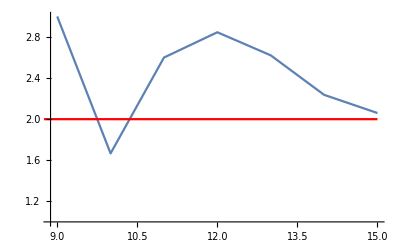
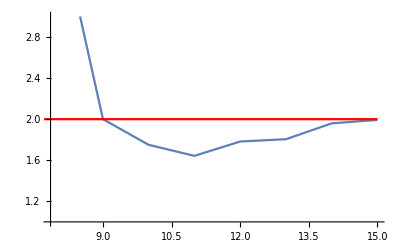
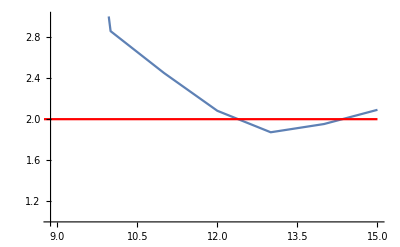
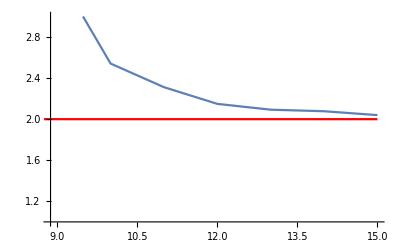
{-Graphics-1000.,-Graphics-1001.,-Graphics-1003.,-Graphics-1004.,-Graphics-1006.,-Graphics-1007.,-Graphics-1009.,-Graphics-1010.,-Graphics-1012.,-Graphics-1013.,-Graphics-1015.,-Graphics-1016.,-Graphics-1018.,-Graphics-1019.,-Graphics-1021.,-Graphics-1022.,-Graphics-1024.,-Graphics-1025.,-Graphics-1027.,-Graphics-1028.,-Graphics-1030.}

```mathematica
Table[Labeled[Show[ListLinePlot[Table[CountConnected2[k,pow,17],{pow,2,17}]//Ratios,PlotRange->{All,{1,3}}],Plot[2,{x,0,15}, PlotStyle->Red]],k],{k,Select[Range[1000,1030],!Divisible[#,3]&]}]//N
```

```mathematica
CountConnected[40,11]
```

963

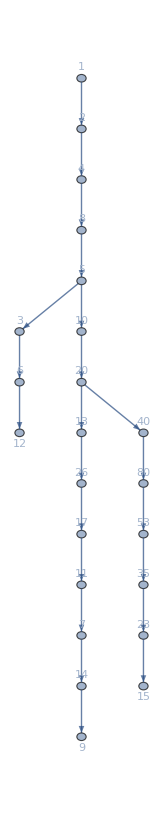

```mathematica
Graph[CollatzForest[30], VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
{{□}, {□}}
```

```mathematica
Monitor[Table[Put[CollatzForest[2^k],"c:\\Saved\\collatz"<>ToString[k]<>".m"],{k,5,17}],k]
```

$Aborted